```mathematica
OutPutPath="ParralelD10";
SetDirectory[NotebookDirectory[]];
$P=2^31-1;
diffInvariants={mt2,s12,s123,s23,s234,s34,s345,s45,s56};
For[i=1,i<=9,i++,			
dhxbMatrices[diffInvariants[[i]]]=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/DEmatrix_d``",OutPutPath,diffInvariants[[i]]]]}]];
]
phasespacepoints=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/parameters",OutPutPath]]}]];
RationalReconstruct[a_]:=With[{v=LatticeReduce[{{a,1},{$P,0}}][[1]]},v[[1]]/v[[2]]];
PureIntegralsNEW=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasis1-111.txt"}]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
```

```mathematica
powerReconstruct[pars_,FitVecIn_]:=Module[{pars2,AnsatzPowersNumi,FitVec,AnsatzPowersDeno,MatNumiPart,onevc,parsCutOne,reconstructedFit,AnsatzPowersDenoOne,
fit,solrule,MatDenoPart,Solset,FinalMat,sol3,Ansatz,MaxPower},
	MaxPower=9;
AnsatzPowersNumi=FrobeniusSolve[{1,1},MaxPower];
	AnsatzPowersDeno=FrobeniusSolve[{1,1},MaxPower];
	pars2=pars/.{x_Integer:>{x,1}};
	(*MatNumiPart=Parallelize@Outer[m31ExpDot,pars2,AnsatzPowersNumi,1];*)

	MatNumiPart=Table[Table[Times@@PowerMod[pars2[[i]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}],{i,1,Length[pars2]}];
	(*Table[Times@@PowerMod[pars2[[1]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}]//Echo;*)
	
	FitVec=Expand[-FitVecIn,Modulus->$P];
	onevc=Table[{1},MaxPower+1];
	parsCutOne=MapThread[Join,{pars2,Transpose[{FitVec}]}];
	AnsatzPowersDenoOne=MapThread[Join,{AnsatzPowersDeno,onevc}];

	(*MatDenoPart=Parallelize@Outer[m31ExpDot,parsCutOne,AnsatzPowersDenoOne,1];*)
	
	MatDenoPart=Table[Table[Times@@PowerMod[parsCutOne[[i]],AnsatzPowersDenoOne[[j]],$P],{j,1,Length[AnsatzPowersDenoOne]}],{i,1,Length[parsCutOne]}];
	
	FinalMat=Expand[MapThread[Join,{MatNumiPart,MatDenoPart}],Modulus->$P];

	
	sol3=NullSpace[FinalMat,Modulus->$P];
	Ansatz=Sum[fac[n]t^n,{n,0,MaxPower}]/Sum[fac[n+MaxPower+1]t^n,{n,0,MaxPower}];
	Solset=Cases[Ansatz,fac[___],Infinity];
	solrule=Thread[Rule[Solset,sol3[[1]]]];
	fit=Together[Ansatz/.solrule]//ExpandDenominator//ExpandNumerator;
	Return[Expand[fit,Modulus->$P]]
]
```

```mathematica
LaunchKernels[20];
```

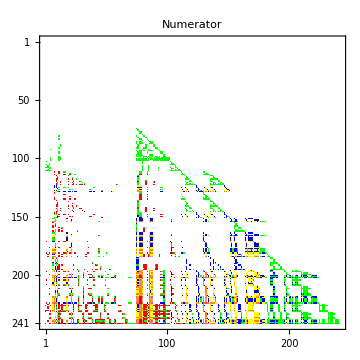
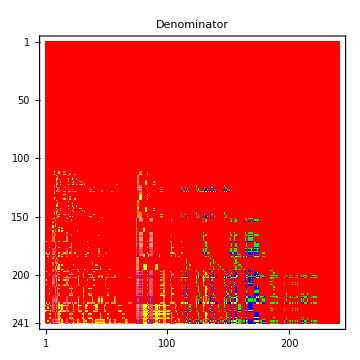
-Graphics- | -Graphics- |

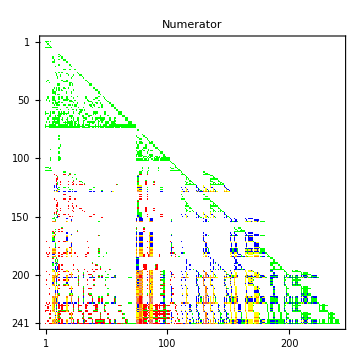
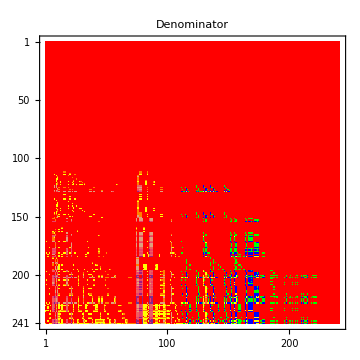
-Graphics- | -Graphics- |

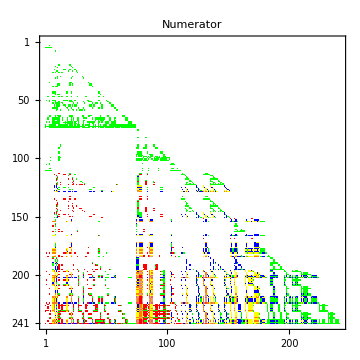
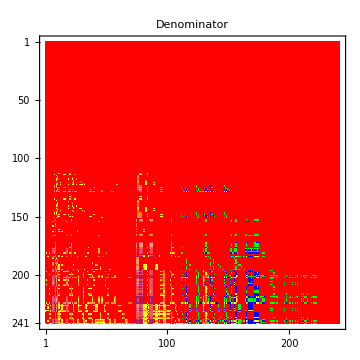
-Graphics- | -Graphics- |

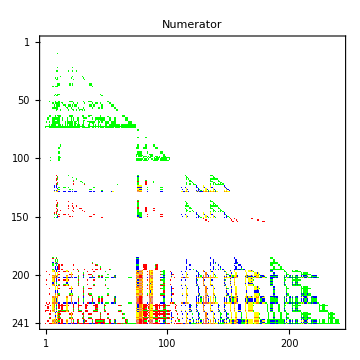
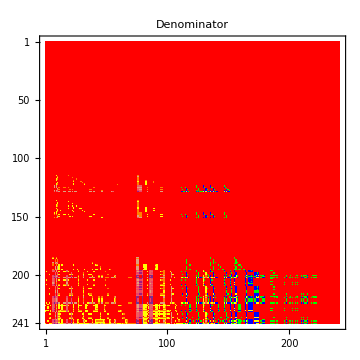
-Graphics- | -Graphics- |

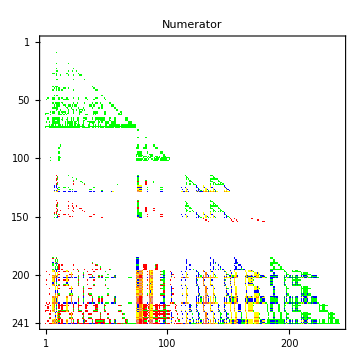
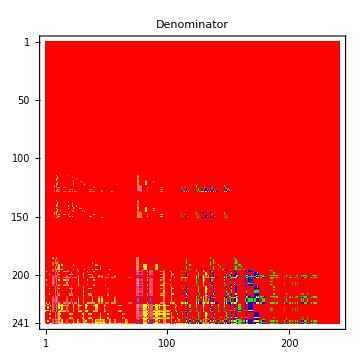
-Graphics- | -Graphics- |

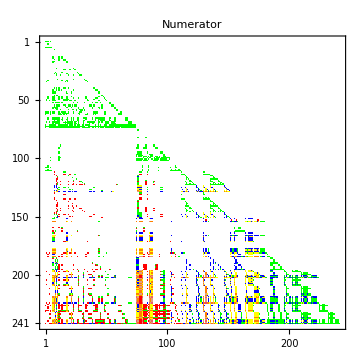
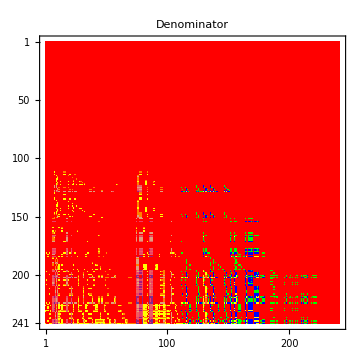
-Graphics- | -Graphics- |

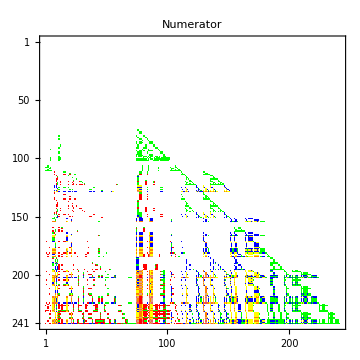
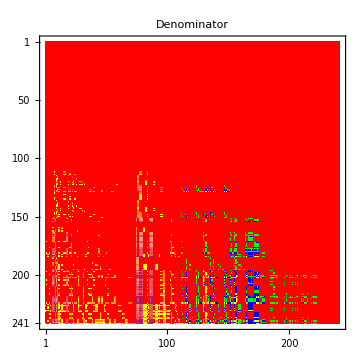
-Graphics- | -Graphics- |

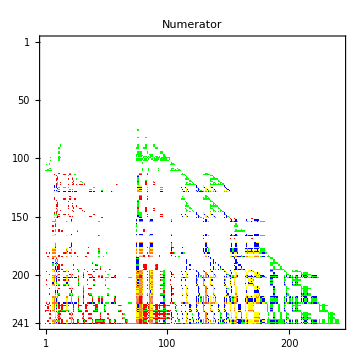
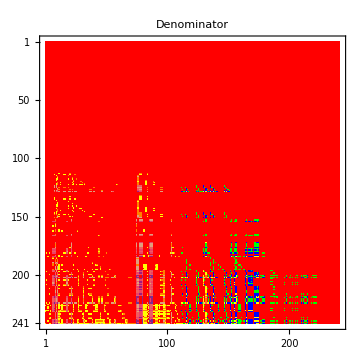
-Graphics- | -Graphics- |

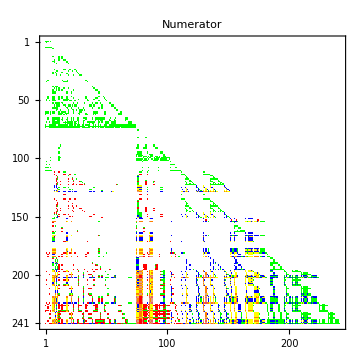
-Graphics- | -Graphics- |

```mathematica
colors={-1->White,0->Red,1->Green,2->Blue,3->Yellow,4->Orange,5->RGBColor["#e09f7d"],6->RGBColor["#EF5D60"],7->RGBColor["#EC4067"],8->RGBColor["#A01A7D"],9->RGBColor["#703399"],10->RGBColor["#0B050F"]};
CutsA=1;
CutsB=241;
For[i=1,i<=9,i++,
MatReco[diffInvariants[[i]]]=ParallelTable[Quiet[Expand[powerReconstruct[phasespacepoints[[All,1]],dhxbMatrices[diffInvariants[[i]]][[All,pos]]]/.{t->4-2ϵ},Modulus->$P]],{pos,1,Length[dhxbMatrices[s234][[1]]]}];
NumiPowers=Exponent[Numerator[MatReco[diffInvariants[[i]]]],ϵ]/.{-Infinity->-1};
DenoPowers=Exponent[Denominator[MatReco[diffInvariants[[i]]]],ϵ];
NumiPowersMat=NumiPowers//Normal;
DenoPowersMat=DenoPowers//Normal;
(*NonZerosPos=ReadList[FileNameJoin[{NotebookDirectory[],"files/NonZeroList.txt"}]];
NumiPowersMat=ConstantArray[-1,241^2];
NumiPowersMat[[NonZerosPos]]=NumiPowers;
DenoPowersMat=ConstantArray[-1,241^2];
DenoPowersMat[[NonZerosPos]]=DenoPowers;*)
P1=MatrixPlot[ArrayReshape[NumiPowersMat,{241,241}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Numerator",ImageSize->Medium];
P2=MatrixPlot[ArrayReshape[DenoPowersMat,{241,241}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Denominator",ImageSize->Medium];
L1=SwatchLegend[Values@colors[[2;;]],Keys@colors[[2;;]],LegendFunction->"Frame",LegendLayout->"Column",LegendLabel->diffInvariants[[i]]];
Print[Grid[{{P1,P2,L1}}]];
]
```

```mathematica
(*ArrayReshape[dhxbMatrices[diffInvariants[[2]]][[1]],{31,31}][[1,68]]
ArrayReshape[dhxbMatrices[diffInvariants[[2]]][[2]],{31,31}][[1,68]]
ArrayReshape[dhxbMatrices[diffInvariants[[2]]][[3]],{31,31}][[1,68]]

ArrayReshape[MatReco[diffInvariants[[2]]],{31,31}][[1,68]]
dhxbMatrices[diffInvariants[[2]]][[All,68]]
powerReconstruct[phasespacepoints[[All,1]],dhxbMatrices[diffInvariants[[6]]][[All,30]]]*)
(*ArrayReshape[MatReco[diffInvariants[[9]]],{31,31}][[22,22]]*)
pos=23;
ArrayReshape[MatReco[diffInvariants[[1]]],{241,241}]//MatrixForm;
TestMat=ArrayReshape[MatReco[diffInvariants[[1]]],{241,241}];
```

```mathematica
EpsUmat=ConstantArray[1,241];
EpsUmat=DiagonalMatrix[EpsUmat];
```

# Integral 112,113,115 (Eps Stucture)

```mathematica
PureIntegralsNEW[[8]]
PureIntegralsNEW[[16]]
PureIntegralsNEW[[112]]
MatE1=ArrayReshape[MatReco[diffInvariants[[1]]],{241,241}][[112,8]]
MatE2=ArrayReshape[MatReco[diffInvariants[[1]]],{241,241}][[112,16]]
Factor[Denominator[MatE1],Modulus->$P]
Factor[Denominator[MatE2],Modulus->$P]
```

((2 ep-13 ep^2+27 ep^3-18 ep^4) hxb[0,0,1,1,0,0,1,0,0,0,0,0,0])/s34

ep^3 hxb[0,0,1,2,0,0,1,0,1,0,0,0,0] root[(-s12+s34)^2-2 (s12+s34) s56+s56^2]

hxb[-1,0,1,1,0,0,1,1,1,0,0,0,0]

234129956/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3)

(38676930+454918932 ϵ)/(1789569706 ϵ^2+1789569705 ϵ^3+ϵ^4)

ϵ (715827882+ϵ) (1073741823+ϵ)

ϵ^2 (715827882+ϵ) (1073741823+ϵ)

```mathematica
RationalReconstruct[715827882]
RationalReconstruct[1073741823]
```

-1/3

-1/2

```mathematica
Factor[Solve[MatE1 x== Numerator[MatE1]*ϵ,x,Modulus->$P],Modulus->$P]
```

{{x→ϵ^2 (715827882+ϵ) (1073741823+ϵ)}}

```mathematica
EpsilonFactor=ϵ^2 (ϵ-1/3) (ϵ-1/2)

EpsUmat[[112,112]]=EpsilonFactor;
EpsUmat[[113,113]]=EpsilonFactor;
EpsUmat[[115,115]]=EpsilonFactor;
```

(-1/2+ϵ) (-1/3+ϵ) ϵ^2

# Integral 114

```mathematica
MatE1=ArrayReshape[MatReco[diffInvariants[[1]]],{241,241}][[114,8]]
RationalReconstruct[1073741823]
Factor[Solve[MatE1 x== Numerator[MatE1]*ϵ,x,Modulus->$P],Modulus->$P]
EpsilonFactor=ϵ^3(ϵ-1/2)
EpsUmat[[114,114]]=EpsilonFactor;
```

1352370493/(1073741823 ϵ^2+ϵ^3)

-1/2

{{x→ϵ^3 (1073741823+ϵ)}}

(-1/2+ϵ) ϵ^3

# Integral 116 (Broken)

```mathematica
TestMat[[116,;;115]]
```

{0,0,0,0,0,0,0,0,0,0,(262731086+1404721649 ϵ)/(238609294 ϵ+596523236 ϵ^2+1073741822 ϵ^3+ϵ^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1908266741+632553600 ϵ+1923284237 ϵ^2)/(238609294 ϵ^2+596523236 ϵ^3+1073741822 ϵ^4+ϵ^5),(2027875194+579896602 ϵ+1035420377 ϵ^2)/(238609294 ϵ^2+596523236 ϵ^3+1073741822 ϵ^4+ϵ^5),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Fac=Factor[238609294 ϵ+596523236 ϵ^2+1073741822 ϵ^3+ϵ^4,Modulus->$P]
EpsilonFactor=Fac/.n_Integer:>RationalReconstruct[n];
EpsUmat[[116,116]]=1
```

ϵ (715827882+ϵ) (1073741823+ϵ) (1431655764+ϵ)

1

# Integral 117

```mathematica
TestMat[[117,;;115]]
```

{0,0,0,0,0,0,0,0,0,0,259016271/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),0,0,0,0,0,0,0,0,0,0,0,(1951984514+1938879014 ϵ)/(1789569706 ϵ^2+1789569705 ϵ^3+ϵ^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1028397292+1169827082 ϵ)/(1789569706 ϵ^2+1789569705 ϵ^3+ϵ^4),(514198646+1321746045 ϵ)/(1789569706 ϵ^2+1789569705 ϵ^3+ϵ^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Fac=ϵ Factor[1789569706 ϵ+1789569705 ϵ^2+ϵ^3,Modulus->$P]
EpsilonFactor=Fac/.n_Integer:>RationalReconstruct[n];
EpsUmat[[117,117]]=EpsilonFactor
```

ϵ^2 (715827882+ϵ) (1073741823+ϵ)

(-1/2+ϵ) (-1/3+ϵ) ϵ^2

# Integral 118 (Broken)

```mathematica
TestMat[[118,;;118]]
```

{0,0,0,0,0,0,0,0,0,819726892/(1073741823 ϵ^2+ϵ^3),1038521746/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),0,0,0,0,0,0,0,0,400192222/(1073741823 ϵ^2+ϵ^3),0,0,1028487399/(1073741823 ϵ^2+ϵ^3),0,0,(1799448603+348035044 ϵ)/(1073741823 ϵ^3+ϵ^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1347043182+1026297862 ϵ)/(1789569706 ϵ^2+1789569705 ϵ^3+ϵ^4),(673521591+951522113 ϵ)/(1789569706 ϵ^2+1789569705 ϵ^3+ϵ^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,783532107+1944370973 ϵ,783987579+2045244102 ϵ,1776191869+1113875334 ϵ,102918897+518894313 ϵ}

```mathematica
Fac=ϵ Factor[1073741823 ϵ^2+ϵ^3,Modulus->$P]
EpsilonFactor=Fac/.n_Integer:>RationalReconstruct[n]
(*Fac=ϵ Factor[1789569706 ϵ+1789569705 ϵ^2+ϵ^3,Modulus->$P]
EpsilonFactor=Fac/.n_Integer:>RationalReconstruct[n]*)
EpsUmat[[118,118]]=1
```

ϵ^3 (1073741823+ϵ)

(-1/2+ϵ) ϵ^3

1

# Integral 119

```mathematica
TestMat[[119,;;119]]
```

{0,0,0,0,0,0,0,0,0,496680490/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),0,0,0,0,0,0,0,0,0,0,0,0,0,(858692211+1301947419 ϵ)/(1789569706 ϵ^2+1789569705 ϵ^3+ϵ^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1175629564+1926062983 ϵ)/(1789569706 ϵ^2+1789569705 ϵ^3+ϵ^4),(948509817+706239949 ϵ)/(1789569706 ϵ^2+1789569705 ϵ^3+ϵ^4),0,0,0,0,0,(1442780140+112161644 ϵ)/(1789569706 ϵ^2+1789569705 ϵ^3+ϵ^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1791080013+139089899 ϵ}

```mathematica
Fac=ϵ Factor[1789569706 ϵ+1789569705 ϵ^2+ϵ^3,Modulus->$P]
EpsilonFactor=Fac/.n_Integer:>RationalReconstruct[n]
EpsUmat[[119,119]]=EpsilonFactor
```

ϵ^2 (715827882+ϵ) (1073741823+ϵ)

(-1/2+ϵ) (-1/3+ϵ) ϵ^2

(-1/2+ϵ) (-1/3+ϵ) ϵ^2

```mathematica
NonZeros=Position[Exponent[Numerator[TestMat],ϵ],0];
PossibleEpsNumerators=(Table[Denominator[TestMat[[NonZeros[[i]][[1]],NonZeros[[i]][[2]]]]],{i,1,Length[NonZeros]}]//DeleteDuplicates)[[;;-2]]
Factor[PossibleEpsNumerators,Modulus->$P]/.n_Integer:>RationalReconstruct[n]
```

{1789569706 ϵ+1789569705 ϵ^2+ϵ^3,1073741823 ϵ^2+ϵ^3,1753426466 ϵ^2+ϵ^3,ϵ^3,482815857 ϵ+1414863958 ϵ^2+ϵ^3}

{(-1/2+ϵ) (-1/3+ϵ) ϵ,(-1/2+ϵ) ϵ^2,(-30065/3357+ϵ) ϵ^2,ϵ^3,(-48800/3453+ϵ) (-1/3+ϵ) ϵ}

```mathematica
NonZeros[[788-18]]
Position[ArrayReshape[MatReco[diffInvariants[[9]]],{241,241}],1]
```

{241,78}

{{200,78},{200,79},{201,78},{201,79},{202,78},{202,79},{218,78},{218,79},{219,78},{219,79},{220,78},{220,79},{221,78},{221,79},{222,78},{222,79},{223,78},{223,79},{224,78},{224,79},{238,78},{238,79},{239,78},{239,79},{240,78},{240,79},{241,78},{241,79}}

# EpsFacs: (-1/2+ϵ) (-1/3+ϵ) ϵ^2

```mathematica
Positions=Position[TestMat,1789569706 ϵ+1789569705 ϵ^2+ϵ^3][[All,;;2]]
Table[TestMat[[Positions[[i]][[1]],Positions[[i]][[2]]]],{i,1,Length[Positions]}]
Fac=ϵ Factor[1789569706 ϵ+1789569705 ϵ^2+ϵ^3,Modulus->$P]
EpsilonFactor=Fac/.n_Integer:>RationalReconstruct[n]
MasterIntPos=Positions[[All,1]]//DeleteDuplicates;
MasterIntPos=DeleteElements[MasterIntPos,{118}]
For[i=1,i<=Length[MasterIntPos],i++,
EpsUmat[[MasterIntPos[[i]],MasterIntPos[[i]]]]=EpsilonFactor;
]
```

{{112,8},{112,12},{113,12},{115,10},{117,11},{118,11},{119,10},{130,8},{136,10},{138,11},{139,11},{140,11},{141,11},{155,7},{157,9},{158,9},{159,7},{159,12}}

{234129956/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),110949142/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),1320857536/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),1030793681/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),259016271/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),1038521746/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),496680490/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),677815127/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),2129227207/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),1389230074/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),1687778935/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),1389974346/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),1747428845/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),502213562/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),1868800660/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),39847908/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),323664277/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),450998478/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3)}

ϵ^2 (715827882+ϵ) (1073741823+ϵ)

(-1/2+ϵ) (-1/3+ϵ) ϵ^2

{112,113,115,117,119,130,136,138,139,140,141,155,157,158,159}

# EpsFacs (-1/2+ϵ) ϵ^3

```mathematica
PosibleNumi=1073741823 ϵ^2+ϵ^3
Positions=Position[TestMat,PosibleNumi][[All,;;2]]
Fac=ϵ Factor[PosibleNumi,Modulus->$P]
EpsilonFactor=Fac/.n_Integer:>RationalReconstruct[n]
MasterIntPos2=Positions[[All,1]]//DeleteDuplicates;
MasterIntPos2=DeleteElements[MasterIntPos2,{118}]
For[i=1,i<=Length[MasterIntPos2],i++,
EpsUmat[[MasterIntPos2[[i]],MasterIntPos2[[i]]]]=EpsilonFactor;
]
Intersection[MasterIntPos2,MasterIntPos]
```

1073741823 ϵ^2+ϵ^3

{{114,8},{114,16},{114,17},{114,21},{114,78},{114,79},{114,84},{118,10},{118,20},{118,23},{120,10},{120,13},{120,20},{120,24},{120,29},{120,76},{120,77},{120,83},{120,90},{121,13},{121,23},{121,83},{121,90},{122,10},{122,24},{122,83},{123,10},{123,13},{123,20},{123,23},{123,24},{123,26},{123,29},{123,30},{123,31},{123,33},{123,59},{123,83},{123,89},{123,90},{131,16},{131,17},{131,78},{131,79},{131,84},{132,78},{132,79},{133,21},{133,78},{133,79},{133,84},{134,8},{134,78},{134,79},{135,8},{135,16},{135,17},{135,21},{135,25},{135,78},{135,79},{135,84},{137,20},{137,76},{137,77},{139,23},{140,10},{141,10},{141,20},{141,23},{141,26},{142,24},{142,76},{142,77},{142,83},{143,10},{143,13},{143,20},{143,24},{143,29},{143,30},{143,76},{143,77},{143,83},{143,89},{143,90},{144,83},{145,13},{145,23},{145,31},{145,83},{145,89},{145,90},{146,10},{146,24},{146,33},{146,83},{158,7},{160,14},{160,15},{160,75},{160,81},{160,82},{161,12},{161,81},{161,82},{162,7},{162,12},{162,14},{162,15},{162,81},{162,82},{163,7},{163,12},{163,14},{163,15},{163,27},{163,81},{163,82},{186,7},{186,10}}

ϵ^3 (1073741823+ϵ)

(-1/2+ϵ) ϵ^3

{114,120,121,122,123,131,132,133,134,135,137,139,140,141,142,143,144,145,146,158,160,161,162,163,186}

{139,140,141,158}

# Test

```mathematica
EpsUmatInv=Inverse[EpsUmat];
TestMat=ArrayReshape[MatReco[diffInvariants[[1]]],{241,241}];
NewMat=Expand[EpsUmat.TestMat.EpsUmatInv,Modulus->$P];
For[i=1,i<=Length[MasterIntPos],i++,
MasterIntPos[[i]]//Echo;
NewMat[[MasterIntPos[[i]],;;MasterIntPos[[i]]]]//Echo;
]
For[i=1,i<=Length[MasterIntPos2],i++,
MasterIntPos2[[i]]//Echo;
NewMat[[MasterIntPos2[[i]],;;MasterIntPos2[[i]]]]//Echo;
]
```

112

{0,0,0,0,0,0,0,234129956 ϵ,0,0,0,110949142 ϵ,0,0,0,38676930+454918932 ϵ,1433081995+286466350 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,681314797+516343112 ϵ,1414399222+2065971210 ϵ,0,0,0,0,1411193223+147922624 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,42714270+1790005847 ϵ}

113

{0,0,0,0,0,0,0,0,0,0,0,1320857536 ϵ,0,0,0,0,0,0,0,0,1848093619+1445985117 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,28238242+270807592 ϵ,14119121+842791868 ϵ,0,0,0,0,523186681+624268135 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,294724846+429481373 ϵ}

115

{0,0,0,0,0,0,0,0,0,1030793681 ϵ,0,0,0,0,0,0,0,0,0,490384096+366070869 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,519114646+529613245 ϵ,259557323+666855246 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1159553069+298016603 ϵ}

117

{0,0,0,0,0,0,0,0,0,0,259016271 ϵ,0,0,0,0,0,0,0,0,0,0,0,1951984514+1938879014 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1028397292+1169827082 ϵ,514198646+1321746045 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2134538492 ϵ^2+1157885331 ϵ^3+898982231 ϵ^4+116506395 ϵ^5,1580979961+1792099109 ϵ}

119

{0,0,0,0,0,0,0,0,0,496680490 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,858692211+1301947419 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1175629564+1926062983 ϵ,948509817+706239949 ϵ,0,0,0,0,0,1442780140+112161644 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1791080013+139089899 ϵ}

130

{0,0,0,0,0,0,0,677815127 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,848175662+932670624 ϵ,424087831+824279303 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,794086678+45280066 ϵ}

136

{0,0,0,0,0,0,0,0,0,2129227207 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1334454961+1293209837 ϵ,1740969304+1759777611 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1564278825+652379419 ϵ}

138

{0,0,0,0,0,0,0,0,0,0,1389230074 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1727959294+1524771190 ϵ,863979647+2113586874 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1269912394 ϵ^2+335504027 ϵ^3+2111431790 ϵ^4+1455690336 ϵ^5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1203986598+1385520232 ϵ}

139

{0,0,0,0,0,0,0,0,0,0,(1687778935 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,1269367466 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15526134 ϵ+1139997709 ϵ^2)/(715827882+ϵ),(7763067 ϵ+1719138755 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1996405867 ϵ^3+528772230 ϵ^4+1694250307 ϵ^5,952476910 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1490195844 ϵ+1318496257 ϵ^2)/(715827882+ϵ),349709516+2024693041 ϵ}

140

{0,0,0,0,0,0,0,0,0,1019693151 ϵ,(1389974346 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(75516336 ϵ+992167708 ϵ^2)/(715827882+ϵ),(37758168 ϵ+1025477715 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,938939044 ϵ^3+1008680640 ϵ^4+669333485 ϵ^5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1440131352 ϵ,0,(2032738461 ϵ+586567956 ϵ^2)/(715827882+ϵ),0,819245719+526398511 ϵ}

141

{0,0,0,0,0,0,0,0,0,610944403 ϵ,(1747428845 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,2101440814 ϵ,0,0,1276264942 ϵ,0,0,1518759166 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(245681855 ϵ+1441712926 ϵ^2)/(715827882+ϵ),(1196582751 ϵ+1327384389 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1766531222 ϵ,1441297859 ϵ^3+324166611 ϵ^4+28926283 ϵ^5,1657612321 ϵ,447504018 ϵ^4+1252475611 ϵ^5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,960305898 ϵ,1746076264+1515249 ϵ,(1553863709 ϵ+1260512150 ϵ^2)/(715827882+ϵ),1368359261+237933383 ϵ,601700287 ϵ,819245719+1833566306 ϵ}

155

{0,0,0,0,0,0,502213562 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,343256962+774455799 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,175883750+1281685922 ϵ}

157

{0,0,0,0,0,0,0,0,1868800660 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,843748112+919974846 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,476573139 ϵ^2+123500067 ϵ^3+1065028259 ϵ^4+5809043 ϵ^5,1508295+1224087128 ϵ}

158

{0,0,0,0,0,0,727338570 ϵ,0,(39847908 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1070999359 ϵ+10969858 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1944370973 ϵ,2106155793 ϵ^3+144647489 ϵ^4+2023500085 ϵ^5,(204475509 ϵ+538108047 ϵ^2)/(715827882+ϵ),819245719+1950051138 ϵ}

159

{0,0,0,0,0,0,323664277 ϵ,0,0,0,0,450998478 ϵ,0,1442470255+1520403972 ϵ,1472377302+1617207874 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,644791342+2127171457 ϵ,0,0,0,0,0,1691722976+474832061 ϵ,399806012+690748111 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1500107230+647376417 ϵ,0,0,0,1011156453+1975693938 ϵ}

114

{0,0,0,0,0,0,0,1352370493 ϵ,0,0,0,0,0,0,0,2047275691 ϵ,730718929 ϵ,0,0,0,1111371572 ϵ,0,0,0,573233180+466583171 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1250664674 ϵ,625332337 ϵ,0,0,0,0,2062228828 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,358152336 ϵ,1910134553 ϵ,1306074548+1183857322 ϵ}

120

{0,0,0,0,0,0,0,0,0,1457142398 ϵ,0,0,583134535 ϵ,0,0,0,0,0,0,234722541 ϵ,0,0,0,159617837 ϵ,0,0,0,0,690341249 ϵ,621309393+810410927 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1613795715 ϵ,595250830 ϵ,0,0,0,0,0,375964051 ϵ,0,0,0,0,0,707935762+305621415 ϵ,217167548 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,154366389 ϵ,0,0,0,1590574507 ϵ,131922243+710507865 ϵ}

121

{0,0,0,0,0,0,0,0,0,0,(624612842 ϵ+1821486996 ϵ^2)/(715827882+ϵ),0,623741306 ϵ,0,0,0,0,0,0,0,0,0,1561201117 ϵ,0,0,0,0,0,0,0,162583128+1984900519 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(634358240 ϵ+445000191 ϵ^2)/(715827882+ϵ),(1770333668 ϵ+2059999678 ϵ^2)/(715827882+ϵ),0,0,0,0,0,570299091 ϵ,0,0,0,0,0,704221166+26250212 ϵ,1275329202 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,819814681 ϵ^3+351874087 ϵ^4+311960396 ϵ^5,1210968816 ϵ,0,0,0,630713369+1737278467 ϵ}

122

{0,0,0,0,0,0,0,0,0,1301685382 ϵ,(670613124 ϵ+1441432463 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,1452876872 ϵ,0,0,0,0,0,0,0,0,1333148329+189287452 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1003811662 ϵ+1360646559 ϵ^2)/(715827882+ϵ),(150390951 ϵ+1678073607 ϵ^2)/(715827882+ϵ),0,0,0,0,0,2070694913 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,801385486 ϵ^3+1490118093 ϵ^4+256672811 ϵ^5,0,0,1969965261 ϵ,0,0,345845075+1218236145 ϵ}

123

{0,0,0,0,0,0,0,0,0,777514382 ϵ,(1322691807 ϵ+1821827478 ϵ^2)/(715827882+ϵ),0,1438047891 ϵ,0,0,0,0,0,0,730308964 ϵ,0,0,1281218023 ϵ,2046675447 ϵ,0,1978024042 ϵ,0,0,1965881551 ϵ,435546680 ϵ,573680503 ϵ,0,1807555230 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1753977748 ϵ,100428579+242847538 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(590008280 ϵ+649059568 ϵ^2)/(715827882+ϵ),(1556412245 ϵ+41337657 ϵ^2)/(715827882+ϵ),0,0,0,0,0,229746754 ϵ,0,0,0,0,0,1317057318 ϵ,1370387149 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,996035173 ϵ,1567084817 ϵ^3+2031395905 ϵ^4+406287157 ϵ^5,525854330 ϵ,1268787648 ϵ^4+1757391998 ϵ^5,1283897839 ϵ,1099956315 ϵ,316961094 ϵ,1297826642 ϵ,793759921+92855984 ϵ}

131

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,43454885 ϵ,1156270350 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2111432941 ϵ,2129458294 ϵ,0,0,0,0,656983101 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1838750869 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,940837093 ϵ,1982026011+632737299 ϵ}

132

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1483364683 ϵ,1815424165 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1328237928+310253510 ϵ}

133

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,293172959 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1611457616 ϵ,805728808 ϵ,0,0,0,0,1414617462 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1873029662 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1658397980+1467257001 ϵ,2045124158+824256882 ϵ}

134

{0,0,0,0,0,0,0,1024695361 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,848338721 ϵ,1497911184 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1940360333 ϵ,0,1715327940+1296467121 ϵ,0,819245719+1449668567 ϵ}

135

{0,0,0,0,0,0,0,345352064 ϵ,0,0,0,0,0,0,0,1811967325 ϵ,893464466 ϵ,0,0,0,148134109 ϵ,0,0,0,593055846 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2144164904 ϵ,1072082452 ϵ,0,0,0,0,1728012964 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,155413301 ϵ,1095774987 ϵ,780183298 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1625965979 ϵ,380712000+1060895524 ϵ,1530316944+1851500109 ϵ,1484999514+1164433630 ϵ,1220900541 ϵ,819245719+346735173 ϵ}

137

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1854239293 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1915700692 ϵ,957850346 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2068081552 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,368768394 ϵ,75213661+700696959 ϵ}

139

{0,0,0,0,0,0,0,0,0,0,(1687778935 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,1269367466 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15526134 ϵ+1139997709 ϵ^2)/(715827882+ϵ),(7763067 ϵ+1719138755 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1996405867 ϵ^3+528772230 ϵ^4+1694250307 ϵ^5,952476910 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1490195844 ϵ+1318496257 ϵ^2)/(715827882+ϵ),349709516+2024693041 ϵ}

140

{0,0,0,0,0,0,0,0,0,1019693151 ϵ,(1389974346 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(75516336 ϵ+992167708 ϵ^2)/(715827882+ϵ),(37758168 ϵ+1025477715 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,938939044 ϵ^3+1008680640 ϵ^4+669333485 ϵ^5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1440131352 ϵ,0,(2032738461 ϵ+586567956 ϵ^2)/(715827882+ϵ),0,819245719+526398511 ϵ}

141

{0,0,0,0,0,0,0,0,0,610944403 ϵ,(1747428845 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,2101440814 ϵ,0,0,1276264942 ϵ,0,0,1518759166 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(245681855 ϵ+1441712926 ϵ^2)/(715827882+ϵ),(1196582751 ϵ+1327384389 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1766531222 ϵ,1441297859 ϵ^3+324166611 ϵ^4+28926283 ϵ^5,1657612321 ϵ,447504018 ϵ^4+1252475611 ϵ^5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,960305898 ϵ,1746076264+1515249 ϵ,(1553863709 ϵ+1260512150 ϵ^2)/(715827882+ϵ),1368359261+237933383 ϵ,601700287 ϵ,819245719+1833566306 ϵ}

142

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1092139081 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1533371867 ϵ,134870701 ϵ,0,0,0,0,0,1767706364 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1927484005 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1508064867 ϵ,0,0,0,0,0,1700230527+1170558493 ϵ}

143

{0,0,0,0,0,0,0,0,0,1693990068 ϵ,0,0,361446914 ϵ,0,0,0,0,0,0,1219330187 ϵ,0,0,0,2028093450 ϵ,0,0,0,0,453493579 ϵ,1552634695 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,733609003 ϵ,1055013499 ϵ,0,0,0,0,0,2086870727 ϵ,0,0,0,0,0,946776377 ϵ,21369694 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1129679060 ϵ,0,0,0,1040897716 ϵ,1296646572 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,490724650 ϵ,1945215076+2075268122 ϵ,0,0,0,0,994612041+935801651 ϵ,650394616+1881007145 ϵ}

144

{0,0,0,0,0,0,0,0,0,0,(1183208128 ϵ+12035462 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1719120109 ϵ+1398344173 ϵ^2)/(715827882+ϵ),(1652673449 ϵ+343329100 ϵ^2)/(715827882+ϵ),0,0,0,0,0,1220057501 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1825291274 ϵ^3+53931482 ϵ^4+1180906528 ϵ^5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(761866211 ϵ+1847866233 ϵ^2)/(715827882+ϵ),0,0,0,0,0,1408488227 ϵ}

145

{0,0,0,0,0,0,0,0,0,0,(592016364 ϵ+1810808489 ϵ^2)/(715827882+ϵ),0,1445167576 ϵ,0,0,0,0,0,0,0,0,0,1446071762 ϵ,0,0,0,0,0,0,0,1593223302 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1619949866 ϵ+1025078672 ϵ^2)/(715827882+ϵ),(1733896466 ϵ+48059729 ϵ^2)/(715827882+ϵ),0,0,0,0,0,742851505 ϵ,0,0,0,0,0,1810021132 ϵ,468210714 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,495676812 ϵ^3+412614805 ϵ^4+1487030436 ϵ^5,2081650280 ϵ,0,0,0,536896209 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(402563781 ϵ+865430997 ϵ^2)/(715827882+ϵ),47578501+1384045506 ϵ,0,0,0,0,1989285847 ϵ,1031208640+877592009 ϵ}

146

{0,0,0,0,0,0,0,0,0,796872476 ϵ,(428020381 ϵ+448727859 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,1077208252 ϵ,0,0,0,0,0,0,0,0,928172914 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1273884711 ϵ+1872972633 ϵ^2)/(715827882+ϵ),(2142119691 ϵ+1983085917 ϵ^2)/(715827882+ϵ),0,0,0,0,0,1265224797 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,702791153 ϵ^3+761456435 ϵ^4+2108373459 ϵ^5,0,0,1198607807 ϵ,0,0,1403131273 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,1913909362 ϵ,0,(1288434880 ϵ+948474731 ϵ^2)/(715827882+ϵ),0,1645684723 ϵ,0,923874930+244398127 ϵ,0,215315749 ϵ,0,819245719+2107525737 ϵ}

158

{0,0,0,0,0,0,727338570 ϵ,0,(39847908 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1070999359 ϵ+10969858 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1944370973 ϵ,2106155793 ϵ^3+144647489 ϵ^4+2023500085 ϵ^5,(204475509 ϵ+538108047 ϵ^2)/(715827882+ϵ),819245719+1950051138 ϵ}

160

{0,0,0,0,0,0,0,0,0,0,0,0,0,1580820200 ϵ,221878206 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,952417497 ϵ,0,0,0,0,0,707527673 ϵ,742755857 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,154366389 ϵ,0,0,0,786470704 ϵ,720708965+121721143 ϵ}

161

{0,0,0,0,0,0,0,0,(238661488 ϵ+1476127250 ϵ^2)/(715827882+ϵ),0,0,1461327374 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1148940884 ϵ+608919876 ϵ^2)/(715827882+ϵ),0,0,0,0,0,1908630131 ϵ,618787725 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,820562283 ϵ^3+349257480 ϵ^4+314203202 ϵ^5,(1084277686 ϵ+1870518505 ϵ^2)/(715827882+ϵ),0,0,0,220508189 ϵ}

162

{0,0,0,0,0,0,67059464 ϵ,0,(236474290 ϵ+1911009357 ϵ^2)/(715827882+ϵ),0,0,271692132 ϵ,0,1698370638 ϵ,734508233 ϵ,0,0,0,0,0,0,0,0,0,0,0,1042860433+1104623214 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1518300510 ϵ+1782689447 ϵ^2)/(715827882+ϵ),0,0,0,0,0,1486164342 ϵ,1362981995 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2129657240 ϵ^3+1136134248 ϵ^4+2094004426 ϵ^5,(2024026294 ϵ+123457353 ϵ^2)/(715827882+ϵ),273871497+1873612150 ϵ,1940360333 ϵ,1370505007+776978640 ϵ,435500725+1711982922 ϵ,1806457119+462457167 ϵ}

163

{0,0,0,0,0,0,1036284210 ϵ,0,(31396607 ϵ+1624116590 ϵ^2)/(715827882+ϵ),0,0,1436435793 ϵ,0,1337294669 ϵ,2135790381 ϵ,0,0,0,0,0,0,0,0,0,0,0,822241474 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1338048812 ϵ+1170359977 ϵ^2)/(715827882+ϵ),0,0,0,0,0,1943743837 ϵ,120534760 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,996035173 ϵ,1166195294 ϵ^3+213283765 ϵ^4+1351102235 ϵ^5,(814723788 ϵ+967501530 ϵ^2)/(715827882+ϵ),1757391998 ϵ,629930806 ϵ,446233796+653722519 ϵ,316961094 ϵ,1610992190 ϵ,819245719+67370186 ϵ}

186

{0,0,0,0,0,0,1353093776 ϵ,0,0,501145517 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1368743008+967478909 ϵ,590002369+1934957818 ϵ,1368743008+9628563 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1113442871+2068081552 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1034040776+79402095 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,61461399 ϵ^3+1840176652 ϵ^4+368768394 ϵ^5,75213661+700696959 ϵ}

```mathematica
NewMat[[114]]
TestMat[[114]]
```

{0,0,0,0,0,0,0,265037718+1352370493 ϵ,0,0,0,0,0,0,0,33402652+2047275691 ϵ,472254906+730718929 ϵ,0,0,0,1061198574+1111371572 ϵ,0,0,0,(1240578038+1849361221 ϵ+466583171 ϵ^2)/ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1014767540+1250664674 ϵ,507383770+625332337 ϵ,0,0,0,0,28418273+2062228828 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2028099535+358152336 ϵ,794944247+1910134553 ϵ,1306074548+1183857322 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1030925671+1202190281 ϵ,1498075684+1145497263 ϵ,23137533+2078071048 ϵ,1854553914+1563048917 ϵ,476887092+1632959528 ϵ,1463665892+364816946 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,1352370493/(1073741823 ϵ^2+ϵ^3),0,0,0,0,0,0,0,2047275691/(1073741823 ϵ^2+ϵ^3),730718929/(1073741823 ϵ^2+ϵ^3),0,0,0,1111371572/(1073741823 ϵ^2+ϵ^3),0,0,0,(573233180+466583171 ϵ)/(1073741823 ϵ^3+ϵ^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1250664674/(1073741823 ϵ^2+ϵ^3),625332337/(1073741823 ϵ^2+ϵ^3),0,0,0,0,2062228828/(1073741823 ϵ^2+ϵ^3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2028099535+358152336 ϵ,794944247+1910134553 ϵ,1306074548+1183857322 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1030925671+1202190281 ϵ,1498075684+1145497263 ϵ,23137533+2078071048 ϵ,1854553914+1563048917 ϵ,476887092+1632959528 ϵ,1463665892+364816946 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
EpsUmat[[139,139]]
```

```mathematica
TestMat[[139,All]]
```

{0,0,0,0,0,0,0,0,0,0,1687778935/(1789569706 ϵ+1789569705 ϵ^2+ϵ^3),0,0,0,0,0,0,0,0,0,0,0,1269367466/(1073741823 ϵ^2+ϵ^3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15526134+1139997709 ϵ)/(1789569706 ϵ^2+1789569705 ϵ^3+ϵ^4),(7763067+1719138755 ϵ)/(1789569706 ϵ^2+1789569705 ϵ^3+ϵ^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,302155560+1694250307 ϵ,398335579+952476910 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1490195844+1318496257 ϵ,349709516+2024693041 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
NewMat[[139,All]]
```

{0,0,0,0,0,0,0,0,0,0,(1687778935 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,1269367466 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(15526134 ϵ+1139997709 ϵ^2)/(715827882+ϵ),(7763067 ϵ+1719138755 ϵ^2)/(715827882+ϵ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1996405867 ϵ^3+528772230 ϵ^4+1694250307 ϵ^5,952476910 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1490195844 ϵ+1318496257 ϵ^2)/(715827882+ϵ),349709516+2024693041 ϵ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Expand[1269367466 ϵ*(715827882+ϵ)/ϵ,Modulus->$P]
```

1008533276+1269367466 ϵ

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"files/Fitmatrices.m"}],SparseArray[Table[ArrayReshape[MatReco[diffInvariants[[i]]],{241,241}],{i,1,9}]]]
```

/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone/files/Fitmatrices.m